# Tensor operators

## Coordinates

```mathematica
ClearAll[coords,sCoords];
coords={t,x,y,z};
sCoords=Drop[coords,1];
```

## 3 metric, extrinsic curvature lapse and shift

1) Metric is COvariant
2) Extrinsic curvature is COvariant
3) Shift is CONTRAvariant
4) ig is the inverse of covariant metric.

```mathematica
ClearAll[g,k,beta];
g={{gxxL,gxyL,gxzL},{gxyL,gyyL,gyzL},{gxzL,gyzL,gzzL}};
k={{kxxL,kxyL,kxzL},{kxyL,kyyL,kyzL},{kxzL,kyzL,kzzL}};
beta={betaxL,betayL,betazL};

ClearAll[ig];
ig={{igxxL,igxyL,igxzL},{igxyL,igyyL,igyzL},{igxzL,igyzL,igzzL}};

(* Compute the adjoint of a matrix *)
ClearAll[adj];
adj[m_]:=Map[Reverse,Minors[Transpose[m],Length[m]-1],{0,1}]*Table[(-1)^(i+j),{i,Length[m]},{j,Length[m]}]
```

## Lie and covariant derivatives

Conventions:

1) Let f be scalar or tensor component. Then ∂_i f=der[f,sCoords⟦i⟧]

2) Let f be scalar. Then ℒ_β f=β^i∂_i f=LieBeta[f]

3) We Write the covariant derivative only of the partial derivative of Phi.
The spatial covariant derivative D of a covariant tensor f is D_i f_j=∂_i f_j-Γ_ij^k f_k

4) Γ_ij^k=CGamma[k,i,j] is symmetric on the lower indices

```mathematica
ClearAll[LieBeta];
LieBeta[f_]:=Sum[beta⟦i⟧der[f,sCoords⟦i⟧],{i,1,3}];

ClearAll[Γ]
Γ[a_,b_,c_]:=Γ[a,c,b]/;b>c;

ClearAll[sD];
sD[i_,j_]:=der[der[PhiL,sCoords⟦j⟧],sCoords⟦i⟧]-Sum[Γ[l,i,j]der[PhiL,sCoords⟦l⟧],{l,1,3}];

ClearAll[CGamma]
CGamma[i_,j_,k_]:=0.5*FullSimplify[Sum[ig⟦i,l⟧(der[g⟦l,j⟧,sCoords⟦k⟧]+der[g⟦l,k⟧,sCoords⟦j⟧]-der[g⟦j,k⟧,sCoords⟦l⟧]),{l,1,3}]];
```

# Substitution Rules

```mathematica
ClearAll[metricDerivRules]
metricDerivRules={
"der(gxxL,x)"->"d_x_gxx","der(gxxL,y)"->"d_y_gxx","der(gxxL,z)"->"d_z_gxx",
"der(gxyL,x)"->"d_x_gxy","der(gxyL,y)"->"d_y_gxy","der(gxyL,z)"->"d_z_gxy",
"der(gxzL,x)"->"d_x_gxz","der(gxzL,y)"->"d_y_gxz","der(gxzL,z)"->"d_z_gxz",
"der(gyyL,x)"->"d_x_gyy","der(gyyL,y)"->"d_y_gyy","der(gyyL,z)"->"d_z_gyy",
"der(gyzL,x)"->"d_x_gyz","der(gyzL,y)"->"d_y_gyz","der(gyzL,z)"->"d_z_gyz",
"der(gzzL,x)"->"d_x_gzz","der(gzzL,y)"->"d_y_gzz","der(gzzL,z)"->"d_z_gzz"
};
```

```mathematica
ClearAll[alphaDerivRules];
alphaDerivRules={
"der(alpL,x)"->"d_x_alp",
"der(alpL,y)"->"d_y_alp",
"der(alpL,z)"->"d_z_alp"
};
```

```mathematica
ClearAll[phiDerivRules];
phiDerivRules=
{
"der(PhiL,x)"->"d_x_Phi",
"der(PhiL,y)"->"d_y_Phi",
"der(PhiL,z)"->"d_z_Phi",

"der(der(PhiL,x),x)"->"d_xx_Phi",
"der(der(PhiL,x),y)"->"d_xy_Phi",
"der(der(PhiL,x),z)"->"d_xz_Phi",

"der(der(PhiL,y),x)"->"d_xy_Phi",
"der(der(PhiL,y),y)"->"d_yy_Phi",
"der(der(PhiL,y),z)"->"d_yz_Phi",

"der(der(PhiL,z),x)"->"d_xz_Phi",
"der(der(PhiL,z),y)"->"d_yz_Phi",
"der(der(PhiL,z),z)"->"d_zz_Phi"
};
```

```mathematica
ClearAll[kPhiDerivRules];
kPhiDerivRules={
"der(KPhiL,x)"->"d_x_K_Phi",
"der(KPhiL,y)"->"d_y_K_Phi",
"der(KPhiL,z)"->"d_z_K_Phi"
};
```

```mathematica
ClearAll[ΓRules];
ΓRules={
"Γ(1,1,1)"->"Gamma_xxx",
"Γ(1,1,2)"->"Gamma_xxy",
"Γ(1,1,3)"->"Gamma_xxz",
"Γ(1,2,2)"->"Gamma_xyy",
"Γ(1,2,3)"->"Gamma_xyz",
"Γ(1,3,3)"->"Gamma_xzz",

"Γ(2,1,1)"->"Gamma_yxx",
"Γ(2,1,2)"->"Gamma_yxy",
"Γ(2,1,3)"->"Gamma_yxz",
"Γ(2,2,2)"->"Gamma_yyy",
"Γ(2,2,3)"->"Gamma_yyz",
"Γ(2,3,3)"->"Gamma_yzz",

"Γ(3,1,1)"->"Gamma_zxx",
"Γ(3,1,2)"->"Gamma_zxy",
"Γ(3,1,3)"->"Gamma_zxz",
"Γ(3,2,2)"->"Gamma_zyy",
"Γ(3,2,3)"->"Gamma_zyz",
"Γ(3,3,3)"->"Gamma_zzz"
};
```

# Code segments

## Inverse Metric

```mathematica
ClearAll[adjg];
adjg = adj[g];


"gdetL = "<>StringReplace[ToString[FullSimplify[Det[g]],FortranForm],"g"~~x_~~y_~~"L"~~"**2":>"g"~~x~~y~~"L*g"~~x~~y~~"L"]<>";"
"igxxL = ("<>StringReplace[ToString[FullSimplify[adjg⟦1,1⟧],FortranForm],"g"~~x_~~y_~~"L"~~"**2":>"g"~~x~~y~~"L*g"~~x~~y~~"L"]<>")/gdetL;"
"igxyL = ("<>StringReplace[ToString[FullSimplify[adjg⟦1,2⟧],FortranForm],"g"~~x_~~y_~~"L"~~"**2":>"g"~~x~~y~~"L*g"~~x~~y~~"L"]<>")/gdetL;"
"igxzL = ("<>StringReplace[ToString[FullSimplify[adjg⟦1,3⟧],FortranForm],"g"~~x_~~y_~~"L"~~"**2":>"g"~~x~~y~~"L*g"~~x~~y~~"L"]<>")/gdetL;"
"igyyL = ("<>StringReplace[ToString[FullSimplify[adjg⟦2,2⟧],FortranForm],"g"~~x_~~y_~~"L"~~"**2":>"g"~~x~~y~~"L*g"~~x~~y~~"L"]<>")/gdetL;"
"igyzL = ("<>StringReplace[ToString[FullSimplify[adjg⟦2,3⟧],FortranForm],"g"~~x_~~y_~~"L"~~"**2":>"g"~~x~~y~~"L*g"~~x~~y~~"L"]<>")/gdetL;"
"igzzL = ("<>StringReplace[ToString[FullSimplify[adjg⟦3,3⟧],FortranForm],"g"~~x_~~y_~~"L"~~"**2":>"g"~~x~~y~~"L*g"~~x~~y~~"L"]<>")/gdetL;"

ClearAll[adjg];
```

gdetL = -(gxzL*gxzL*gyyL) + 2*gxyL*gxzL*gyzL - gxxL*gyzL*gyzL - gxyL*gxyL*gzzL + gxxL*gyyL*gzzL;

igxxL = (-gyzL*gyzL + gyyL*gzzL)/gdetL;

igxyL = (gxzL*gyzL - gxyL*gzzL)/gdetL;

igxzL = (-(gxzL*gyyL) + gxyL*gyzL)/gdetL;

igyyL = (-gxzL*gxzL + gxxL*gzzL)/gdetL;

igyzL = (gxyL*gxzL - gxxL*gyzL)/gdetL;

igzzL = (-gxyL*gxyL + gxxL*gyyL)/gdetL;

## Christoffel Symbols

```mathematica
ClearAll[a,b,c,symbols];

symbols=
Flatten[
Table[

ToString[Γ[a,b,c],CForm]<>" = "<>StringReplace[ToString[CGamma[a,b,c],CForm],metricDerivRules]<>";",
{a,1,3},
{b,1,3},
{c,1,3}
]
];

TableForm[DeleteDuplicates[StringReplace[#,ΓRules]&/@symbols]]

ClearAll[a,b,c,symbols];
```

Gamma_xxx = 0.5*(igxxL*d_x_gxx - igxyL*d_y_gxx - igxzL*d_z_gxx + 2*igxyL*d_x_gxy + 2*igxzL*d_x_gxz);
Gamma_xxy = 0.5*(igxxL*d_y_gxx + igxyL*d_x_gyy + igxzL*(-d_z_gxy + d_y_gxz + d_x_gyz));
Gamma_xxz = 0.5*(igxxL*d_z_gxx + igxyL*(d_z_gxy - d_y_gxz + d_x_gyz) + igxzL*d_x_gzz);
Gamma_xyy = 0.5*(2*igxxL*d_y_gxy - igxxL*d_x_gyy + igxyL*d_y_gyy - igxzL*d_z_gyy + 2*igxzL*d_y_gyz);
Gamma_xyz = 0.5*(igxyL*d_z_gyy + igxxL*(d_z_gxy + d_y_gxz - d_x_gyz) + igxzL*d_y_gzz);
Gamma_xzz = 0.5*(2*igxxL*d_z_gxz + 2*igxyL*d_z_gyz - igxxL*d_x_gzz - igxyL*d_y_gzz + igxzL*d_z_gzz);
Gamma_yxx = 0.5*(igxyL*d_x_gxx - igyyL*d_y_gxx - igyzL*d_z_gxx + 2*igyyL*d_x_gxy + 2*igyzL*d_x_gxz);
Gamma_yxy = 0.5*(igxyL*d_y_gxx + igyyL*d_x_gyy + igyzL*(-d_z_gxy + d_y_gxz + d_x_gyz));
Gamma_yxz = 0.5*(igxyL*d_z_gxx + igyyL*(d_z_gxy - d_y_gxz + d_x_gyz) + igyzL*d_x_gzz);
Gamma_yyy = 0.5*(2*igxyL*d_y_gxy - igxyL*d_x_gyy + igyyL*d_y_gyy - igyzL*d_z_gyy + 2*igyzL*d_y_gyz);
Gamma_yyz = 0.5*(igyyL*d_z_gyy + igxyL*(d_z_gxy + d_y_gxz - d_x_gyz) + igyzL*d_y_gzz);
Gamma_yzz = 0.5*(2*igxyL*d_z_gxz + 2*igyyL*d_z_gyz - igxyL*d_x_gzz - igyyL*d_y_gzz + igyzL*d_z_gzz);
Gamma_zxx = 0.5*(igxzL*d_x_gxx - igyzL*d_y_gxx - igzzL*d_z_gxx + 2*igyzL*d_x_gxy + 2*igzzL*d_x_gxz);
Gamma_zxy = 0.5*(igxzL*d_y_gxx + igyzL*d_x_gyy + igzzL*(-d_z_gxy + d_y_gxz + d_x_gyz));
Gamma_zxz = 0.5*(igxzL*d_z_gxx + igyzL*(d_z_gxy - d_y_gxz + d_x_gyz) + igzzL*d_x_gzz);
Gamma_zyy = 0.5*(2*igxzL*d_y_gxy - igxzL*d_x_gyy + igyzL*d_y_gyy - igzzL*d_z_gyy + 2*igzzL*d_y_gyz);
Gamma_zyz = 0.5*(igyzL*d_z_gyy + igxzL*(d_z_gxy + d_y_gxz - d_x_gyz) + igzzL*d_y_gzz);
Gamma_zzz = 0.5*(2*igxzL*d_z_gxz + 2*igyzL*d_z_gyz - igxzL*d_x_gzz - igyzL*d_y_gzz + igzzL*d_z_gzz);

## Derivatives

```mathematica
StringReplace[ToString[
FullSimplify[Sum[ig⟦i,j⟧sD[i,j],{i,1,3},{j,1,3}]],
CForm]
,Join[phiDerivRules,ΓRules]]
```

igxxL*d_xx_Phi + igxyL*(d_xy_Phi + d_xy_Phi) + igyyL*d_yy_Phi + igxzL*(d_xz_Phi + d_xz_Phi) + igyzL*(d_yz_Phi + d_yz_Phi) + igzzL*d_zz_Phi - d_x_Phi*(igxxL*Gamma_xxx + 2*igxyL*Gamma_xxy + 2*igxzL*Gamma_xxz + igyyL*Gamma_xyy + 2*igyzL*Gamma_xyz + igzzL*Gamma_xzz) - igxxL*d_y_Phi*Gamma_yxx - 2*igxyL*d_y_Phi*Gamma_yxy - 2*igxzL*d_y_Phi*Gamma_yxz - igyyL*d_y_Phi*Gamma_yyy - 2*igyzL*d_y_Phi*Gamma_yyz - igzzL*d_y_Phi*Gamma_yzz - igxxL*d_z_Phi*Gamma_zxx - 2*igxyL*d_z_Phi*Gamma_zxy - 2*igxzL*d_z_Phi*Gamma_zxz - igyyL*d_z_Phi*Gamma_zyy - 2*igyzL*d_z_Phi*Gamma_zyz - igzzL*d_z_Phi*Gamma_zzz

```mathematica
StringReplace[ToString[FullSimplify[Sum[ig⟦i,j⟧der[alpL,sCoords⟦i⟧]der[PhiL,sCoords⟦j⟧],{i,1,3},{j,1,3}]],CForm],Join[alphaDerivRules,phiDerivRules]]
```

d_x_alp*(igxxL*d_x_Phi + igxyL*d_y_Phi + igxzL*d_z_Phi) + d_y_alp*(igxyL*d_x_Phi + igyyL*d_y_Phi + igyzL*d_z_Phi) + d_z_alp*(igxzL*d_x_Phi + igyzL*d_y_Phi + igzzL*d_z_Phi)

# Finite difference formulas

See http://www.holoborodko.com/pavel/2014/11/04/computing-mixed-derivatives-by-finite-differences

## For the KleinGordon version

```mathematica
ClearAll[grid,size];
size=5;
grid={Table[i,{i,-size,size}]dx,Table[i,{i,-size,size}]dy,Table[i,{i,-size,size}]dz};

ClearAll[values];
values=Flatten[Table[F[a,b,c],{a,grid⟦1⟧},{b,grid⟦2⟧},{c,grid⟦3⟧}]];

ClearAll[derivative];
derivative=FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[1,0,0],grid,values,"DifferenceOrder"->2]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧];

ClearAll[F,k];
F[a_,b_,c_]:=f[II[i+a/dx,j+b/dy,k+c/dz]];
StringReplace[ToString[derivative,CForm],{"f("->"f[","k))"->"k)]","II"->"I"}]

ClearAll[grid,size];
ClearAll[values];
ClearAll[derivative];
ClearAll[F];
```

(-f[I(-1 + i,j,k)] + f[I(1 + i,j,k)])/(2.*dx)

## For the KleinGordonX version

```mathematica
ClearAll[grid,size,order];
size=5;
order=8;
grid={Table[i,{i,-size,size}]dx,Table[i,{i,-size,size}]dy,Table[i,{i,-size,size}]dz};

ClearAll[values];
values=Flatten[Table[F[a,b,c],{a,grid⟦1⟧},{b,grid⟦2⟧},{c,grid⟦3⟧}]];

ClearAll[gradient];
gradient={
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[1,0,0],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[0,1,0],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[0,0,1],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧]
};


ClearAll[hessian];
hessian={
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[2,0,0],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[0,2,0],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[0,0,2],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[1,1,0],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[1,0,1],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧],
FullSimplify[NDSolve`FiniteDifferenceDerivative[Derivative[0,1,1],grid,values,"DifferenceOrder"->order]⟦Position[values,F[0,0,0]]⟦1,1⟧⟧]
};

ClearAll[F];
F[a_,b_,c_]:=gf[pI+a/dx*pDI0+b/dy*pDI1+c/dz*pDI2];

ClearAll[numerator,denominator];

numerator=(StringJoin["(",#,")"]&)/@(StringReplace[#,{"pI"->"p.I","pDI0"->"p.DI[0]","pDI1"->"p.DI[1]","pDI2"->"p.DI[2]"}]&)/@(ToString[#,CForm]&)/@Numerator/@gradient;
denominator=(StringJoin["(1.0 / (",#,"))"]&)/@(StringReplace[#,{"dx"->"p.dx","dy"->"p.dy","dz"->"p.dz"}]&)/@(ToString[#,CForm]&)/@Denominator/@gradient;
Print[MapThread[StringJoin[#1," * ",#2]&,{numerator,denominator}]]

ClearAll[numerator,denominator];

numerator=(StringJoin["(",#,")"]&)/@(StringReplace[#,{"pI"->"p.I","pDI0"->"p.DI[0]","pDI1"->"p.DI[1]","pDI2"->"p.DI[2]"}]&)/@(ToString[#,CForm]&)/@Numerator/@hessian;
denominator=(StringJoin["(1.0 / (",#,"))"]&)/@(StringReplace[#,{"dx"->"p.dx","dy"->"p.dy","dz"->"p.dz"}]&)/@(ToString[#,CForm]&)/@Denominator/@hessian;
denominator=(StringReplace[#,{"Power(p.dx,2)"->"power<2>(p.dx)","Power(p.dy,2)"->"power<2>(p.dy)","Power(p.dz,2)"->"power<2>(p.dz)"}]&)/@denominator;
Print[MapThread[StringJoin[#1," * ",#2]&,{numerator,denominator}]]

ClearAll[grid,size,order];
ClearAll[values];
ClearAll[derivative];
ClearAll[F];
```

{(3*gf(-4*p.DI[0] + p.I) - 32*gf(-3*p.DI[0] + p.I) + 168*(gf(-2*p.DI[0] + p.I) - 4*gf(-p.DI[0] + p.I) + 4*gf(p.DI[0] + p.I) - gf(2*p.DI[0] + p.I)) + 32*gf(3*p.DI[0] + p.I) - 3*gf(4*p.DI[0] + p.I)) * (1.0 / (840*p.dx)),(3*gf(-4*p.DI[1] + p.I) - 32*gf(-3*p.DI[1] + p.I) + 168*(gf(-2*p.DI[1] + p.I) - 4*gf(-p.DI[1] + p.I) + 4*gf(p.DI[1] + p.I) - gf(2*p.DI[1] + p.I)) + 32*gf(3*p.DI[1] + p.I) - 3*gf(4*p.DI[1] + p.I)) * (1.0 / (840*p.dy)),(3*gf(-4*p.DI[2] + p.I) - 32*gf(-3*p.DI[2] + p.I) + 168*(gf(-2*p.DI[2] + p.I) - 4*gf(-p.DI[2] + p.I) + 4*gf(p.DI[2] + p.I) - gf(2*p.DI[2] + p.I)) + 32*gf(3*p.DI[2] + p.I) - 3*gf(4*p.DI[2] + p.I)) * (1.0 / (840*p.dz))}

{(-14350*gf(p.I) - 9*gf(-4*p.DI[0] + p.I) + 128*gf(-3*p.DI[0] + p.I) - 1008*gf(-2*p.DI[0] + p.I) + 8064*gf(-p.DI[0] + p.I) + 8064*gf(p.DI[0] + p.I) - 1008*gf(2*p.DI[0] + p.I) + 128*gf(3*p.DI[0] + p.I) - 9*gf(4*p.DI[0] + p.I)) * (1.0 / (5040*power<2>(p.dx))),(-14350*gf(p.I) - 9*gf(-4*p.DI[1] + p.I) + 128*gf(-3*p.DI[1] + p.I) - 1008*gf(-2*p.DI[1] + p.I) + 8064*gf(-p.DI[1] + p.I) + 8064*gf(p.DI[1] + p.I) - 1008*gf(2*p.DI[1] + p.I) + 128*gf(3*p.DI[1] + p.I) - 9*gf(4*p.DI[1] + p.I)) * (1.0 / (5040*power<2>(p.dy))),(-14350*gf(p.I) - 9*gf(-4*p.DI[2] + p.I) + 128*gf(-3*p.DI[2] + p.I) - 1008*gf(-2*p.DI[2] + p.I) + 8064*gf(-p.DI[2] + p.I) + 8064*gf(p.DI[2] + p.I) - 1008*gf(2*p.DI[2] + p.I) + 128*gf(3*p.DI[2] + p.I) - 9*gf(4*p.DI[2] + p.I)) * (1.0 / (5040*power<2>(p.dz))),(9*gf(-4*p.DI[0] - 4*p.DI[1] + p.I) - 96*gf(-3*p.DI[0] - 4*p.DI[1] + p.I) + 504*gf(-2*p.DI[0] - 4*p.DI[1] + p.I) - 2016*gf(-p.DI[0] - 4*p.DI[1] + p.I) + 2016*gf(p.DI[0] - 4*p.DI[1] + p.I) - 504*gf(2*p.DI[0] - 4*p.DI[1] + p.I) + 96*gf(3*p.DI[0] - 4*p.DI[1] + p.I) - 9*gf(4*p.DI[0] - 4*p.DI[1] + p.I) - 96*gf(-4*p.DI[0] - 3*p.DI[1] + p.I) + 1024*gf(-3*p.DI[0] - 3*p.DI[1] + p.I) - 5376*gf(-2*p.DI[0] - 3*p.DI[1] + p.I) + 21504*gf(-p.DI[0] - 3*p.DI[1] + p.I) - 21504*gf(p.DI[0] - 3*p.DI[1] + p.I) + 5376*gf(2*p.DI[0] - 3*p.DI[1] + p.I) - 1024*gf(3*p.DI[0] - 3*p.DI[1] + p.I) + 96*gf(4*p.DI[0] - 3*p.DI[1] + p.I) + 504*gf(-4*p.DI[0] - 2*p.DI[1] + p.I) - 5376*gf(-3*p.DI[0] - 2*p.DI[1] + p.I) + 28224*gf(-2*p.DI[0] - 2*p.DI[1] + p.I) - 112896*gf(-p.DI[0] - 2*p.DI[1] + p.I) + 112896*gf(p.DI[0] - 2*p.DI[1] + p.I) - 28224*gf(2*p.DI[0] - 2*p.DI[1] + p.I) + 5376*gf(3*p.DI[0] - 2*p.DI[1] + p.I) - 2016*gf(-4*p.DI[0] - p.DI[1] + p.I) + 21504*gf(-3*p.DI[0] - p.DI[1] + p.I) - 112896*gf(-2*p.DI[0] - p.DI[1] + p.I) + 451584*gf(-p.DI[0] - p.DI[1] + p.I) - 451584*gf(p.DI[0] - p.DI[1] + p.I) + 112896*gf(2*p.DI[0] - p.DI[1] + p.I) - 21504*gf(3*p.DI[0] - p.DI[1] + p.I) + 2016*gf(-4*p.DI[0] + p.DI[1] + p.I) - 21504*gf(-3*p.DI[0] + p.DI[1] + p.I) + 112896*gf(-2*p.DI[0] + p.DI[1] + p.I) - 451584*gf(-p.DI[0] + p.DI[1] + p.I) + 451584*gf(p.DI[0] + p.DI[1] + p.I) - 112896*gf(2*p.DI[0] + p.DI[1] + p.I) + 21504*gf(3*p.DI[0] + p.DI[1] + p.I) - 504*gf(-4*p.DI[0] + 2*p.DI[1] + p.I) + 5376*gf(-3*p.DI[0] + 2*p.DI[1] + p.I) - 28224*gf(-2*p.DI[0] + 2*p.DI[1] + p.I) + 112896*gf(-p.DI[0] + 2*p.DI[1] + p.I) - 112896*gf(p.DI[0] + 2*p.DI[1] + p.I) + 28224*gf(2*p.DI[0] + 2*p.DI[1] + p.I) - 5376*gf(3*p.DI[0] + 2*p.DI[1] + p.I) - 504*(gf(4*p.DI[0] - 2*p.DI[1] + p.I) - 4*gf(4*p.DI[0] - p.DI[1] + p.I) + 4*gf(4*p.DI[0] + p.DI[1] + p.I) - gf(4*p.DI[0] + 2*p.DI[1] + p.I)) + 96*gf(-4*p.DI[0] + 3*p.DI[1] + p.I) - 1024*gf(-3*p.DI[0] + 3*p.DI[1] + p.I) + 5376*gf(-2*p.DI[0] + 3*p.DI[1] + p.I) - 21504*gf(-p.DI[0] + 3*p.DI[1] + p.I) + 21504*gf(p.DI[0] + 3*p.DI[1] + p.I) - 5376*gf(2*p.DI[0] + 3*p.DI[1] + p.I) + 1024*gf(3*p.DI[0] + 3*p.DI[1] + p.I) - 96*gf(4*p.DI[0] + 3*p.DI[1] + p.I) - 9*gf(-4*p.DI[0] + 4*p.DI[1] + p.I) + 96*gf(-3*p.DI[0] + 4*p.DI[1] + p.I) - 504*gf(-2*p.DI[0] + 4*p.DI[1] + p.I) + 2016*gf(-p.DI[0] + 4*p.DI[1] + p.I) - 2016*gf(p.DI[0] + 4*p.DI[1] + p.I) + 504*gf(2*p.DI[0] + 4*p.DI[1] + p.I) - 96*gf(3*p.DI[0] + 4*p.DI[1] + p.I) + 9*gf(4*p.DI[0] + 4*p.DI[1] + p.I)) * (1.0 / (705600*p.dx*p.dy)),(9*gf(-4*p.DI[0] - 4*p.DI[2] + p.I) - 96*gf(-3*p.DI[0] - 4*p.DI[2] + p.I) + 504*gf(-2*p.DI[0] - 4*p.DI[2] + p.I) - 2016*gf(-p.DI[0] - 4*p.DI[2] + p.I) + 2016*gf(p.DI[0] - 4*p.DI[2] + p.I) - 504*gf(2*p.DI[0] - 4*p.DI[2] + p.I) + 96*gf(3*p.DI[0] - 4*p.DI[2] + p.I) - 9*gf(4*p.DI[0] - 4*p.DI[2] + p.I) - 96*gf(-4*p.DI[0] - 3*p.DI[2] + p.I) + 1024*gf(-3*p.DI[0] - 3*p.DI[2] + p.I) - 5376*gf(-2*p.DI[0] - 3*p.DI[2] + p.I) + 21504*gf(-p.DI[0] - 3*p.DI[2] + p.I) - 21504*gf(p.DI[0] - 3*p.DI[2] + p.I) + 5376*gf(2*p.DI[0] - 3*p.DI[2] + p.I) - 1024*gf(3*p.DI[0] - 3*p.DI[2] + p.I) + 96*gf(4*p.DI[0] - 3*p.DI[2] + p.I) + 504*gf(-4*p.DI[0] - 2*p.DI[2] + p.I) - 5376*gf(-3*p.DI[0] - 2*p.DI[2] + p.I) + 28224*gf(-2*p.DI[0] - 2*p.DI[2] + p.I) - 112896*gf(-p.DI[0] - 2*p.DI[2] + p.I) + 112896*gf(p.DI[0] - 2*p.DI[2] + p.I) - 28224*gf(2*p.DI[0] - 2*p.DI[2] + p.I) + 5376*gf(3*p.DI[0] - 2*p.DI[2] + p.I) - 2016*gf(-4*p.DI[0] - p.DI[2] + p.I) + 21504*gf(-3*p.DI[0] - p.DI[2] + p.I) - 112896*gf(-2*p.DI[0] - p.DI[2] + p.I) + 451584*gf(-p.DI[0] - p.DI[2] + p.I) - 451584*gf(p.DI[0] - p.DI[2] + p.I) + 112896*gf(2*p.DI[0] - p.DI[2] + p.I) - 21504*gf(3*p.DI[0] - p.DI[2] + p.I) + 2016*gf(-4*p.DI[0] + p.DI[2] + p.I) - 21504*gf(-3*p.DI[0] + p.DI[2] + p.I) + 112896*gf(-2*p.DI[0] + p.DI[2] + p.I) - 451584*gf(-p.DI[0] + p.DI[2] + p.I) + 451584*gf(p.DI[0] + p.DI[2] + p.I) - 112896*gf(2*p.DI[0] + p.DI[2] + p.I) + 21504*gf(3*p.DI[0] + p.DI[2] + p.I) - 504*gf(-4*p.DI[0] + 2*p.DI[2] + p.I) + 5376*gf(-3*p.DI[0] + 2*p.DI[2] + p.I) - 28224*gf(-2*p.DI[0] + 2*p.DI[2] + p.I) + 112896*gf(-p.DI[0] + 2*p.DI[2] + p.I) - 112896*gf(p.DI[0] + 2*p.DI[2] + p.I) + 28224*gf(2*p.DI[0] + 2*p.DI[2] + p.I) - 5376*gf(3*p.DI[0] + 2*p.DI[2] + p.I) - 504*(gf(4*p.DI[0] - 2*p.DI[2] + p.I) - 4*gf(4*p.DI[0] - p.DI[2] + p.I) + 4*gf(4*p.DI[0] + p.DI[2] + p.I) - gf(4*p.DI[0] + 2*p.DI[2] + p.I)) + 96*gf(-4*p.DI[0] + 3*p.DI[2] + p.I) - 1024*gf(-3*p.DI[0] + 3*p.DI[2] + p.I) + 5376*gf(-2*p.DI[0] + 3*p.DI[2] + p.I) - 21504*gf(-p.DI[0] + 3*p.DI[2] + p.I) + 21504*gf(p.DI[0] + 3*p.DI[2] + p.I) - 5376*gf(2*p.DI[0] + 3*p.DI[2] + p.I) + 1024*gf(3*p.DI[0] + 3*p.DI[2] + p.I) - 96*gf(4*p.DI[0] + 3*p.DI[2] + p.I) - 9*gf(-4*p.DI[0] + 4*p.DI[2] + p.I) + 96*gf(-3*p.DI[0] + 4*p.DI[2] + p.I) - 504*gf(-2*p.DI[0] + 4*p.DI[2] + p.I) + 2016*gf(-p.DI[0] + 4*p.DI[2] + p.I) - 2016*gf(p.DI[0] + 4*p.DI[2] + p.I) + 504*gf(2*p.DI[0] + 4*p.DI[2] + p.I) - 96*gf(3*p.DI[0] + 4*p.DI[2] + p.I) + 9*gf(4*p.DI[0] + 4*p.DI[2] + p.I)) * (1.0 / (705600*p.dx*p.dz)),(9*gf(-4*p.DI[1] - 4*p.DI[2] + p.I) - 96*gf(-3*p.DI[1] - 4*p.DI[2] + p.I) + 504*gf(-2*p.DI[1] - 4*p.DI[2] + p.I) - 2016*gf(-p.DI[1] - 4*p.DI[2] + p.I) + 2016*gf(p.DI[1] - 4*p.DI[2] + p.I) - 504*gf(2*p.DI[1] - 4*p.DI[2] + p.I) + 96*gf(3*p.DI[1] - 4*p.DI[2] + p.I) - 9*gf(4*p.DI[1] - 4*p.DI[2] + p.I) - 96*gf(-4*p.DI[1] - 3*p.DI[2] + p.I) + 1024*gf(-3*p.DI[1] - 3*p.DI[2] + p.I) - 5376*gf(-2*p.DI[1] - 3*p.DI[2] + p.I) + 21504*gf(-p.DI[1] - 3*p.DI[2] + p.I) - 21504*gf(p.DI[1] - 3*p.DI[2] + p.I) + 5376*gf(2*p.DI[1] - 3*p.DI[2] + p.I) - 1024*gf(3*p.DI[1] - 3*p.DI[2] + p.I) + 96*gf(4*p.DI[1] - 3*p.DI[2] + p.I) + 504*gf(-4*p.DI[1] - 2*p.DI[2] + p.I) - 5376*gf(-3*p.DI[1] - 2*p.DI[2] + p.I) + 28224*gf(-2*p.DI[1] - 2*p.DI[2] + p.I) - 112896*gf(-p.DI[1] - 2*p.DI[2] + p.I) + 112896*gf(p.DI[1] - 2*p.DI[2] + p.I) - 28224*gf(2*p.DI[1] - 2*p.DI[2] + p.I) + 5376*gf(3*p.DI[1] - 2*p.DI[2] + p.I) - 2016*gf(-4*p.DI[1] - p.DI[2] + p.I) + 21504*gf(-3*p.DI[1] - p.DI[2] + p.I) - 112896*gf(-2*p.DI[1] - p.DI[2] + p.I) + 451584*gf(-p.DI[1] - p.DI[2] + p.I) - 451584*gf(p.DI[1] - p.DI[2] + p.I) + 112896*gf(2*p.DI[1] - p.DI[2] + p.I) - 21504*gf(3*p.DI[1] - p.DI[2] + p.I) + 2016*gf(-4*p.DI[1] + p.DI[2] + p.I) - 21504*gf(-3*p.DI[1] + p.DI[2] + p.I) + 112896*gf(-2*p.DI[1] + p.DI[2] + p.I) - 451584*gf(-p.DI[1] + p.DI[2] + p.I) + 451584*gf(p.DI[1] + p.DI[2] + p.I) - 112896*gf(2*p.DI[1] + p.DI[2] + p.I) + 21504*gf(3*p.DI[1] + p.DI[2] + p.I) - 504*gf(-4*p.DI[1] + 2*p.DI[2] + p.I) + 5376*gf(-3*p.DI[1] + 2*p.DI[2] + p.I) - 28224*gf(-2*p.DI[1] + 2*p.DI[2] + p.I) + 112896*gf(-p.DI[1] + 2*p.DI[2] + p.I) - 112896*gf(p.DI[1] + 2*p.DI[2] + p.I) + 28224*gf(2*p.DI[1] + 2*p.DI[2] + p.I) - 5376*gf(3*p.DI[1] + 2*p.DI[2] + p.I) - 504*(gf(4*p.DI[1] - 2*p.DI[2] + p.I) - 4*gf(4*p.DI[1] - p.DI[2] + p.I) + 4*gf(4*p.DI[1] + p.DI[2] + p.I) - gf(4*p.DI[1] + 2*p.DI[2] + p.I)) + 96*gf(-4*p.DI[1] + 3*p.DI[2] + p.I) - 1024*gf(-3*p.DI[1] + 3*p.DI[2] + p.I) + 5376*gf(-2*p.DI[1] + 3*p.DI[2] + p.I) - 21504*gf(-p.DI[1] + 3*p.DI[2] + p.I) + 21504*gf(p.DI[1] + 3*p.DI[2] + p.I) - 5376*gf(2*p.DI[1] + 3*p.DI[2] + p.I) + 1024*gf(3*p.DI[1] + 3*p.DI[2] + p.I) - 96*gf(4*p.DI[1] + 3*p.DI[2] + p.I) - 9*gf(-4*p.DI[1] + 4*p.DI[2] + p.I) + 96*gf(-3*p.DI[1] + 4*p.DI[2] + p.I) - 504*gf(-2*p.DI[1] + 4*p.DI[2] + p.I) + 2016*gf(-p.DI[1] + 4*p.DI[2] + p.I) - 2016*gf(p.DI[1] + 4*p.DI[2] + p.I) + 504*gf(2*p.DI[1] + 4*p.DI[2] + p.I) - 96*gf(3*p.DI[1] + 4*p.DI[2] + p.I) + 9*gf(4*p.DI[1] + 4*p.DI[2] + p.I)) * (1.0 / (705600*p.dy*p.dz))}

# Smooth transition functions (excision masks)

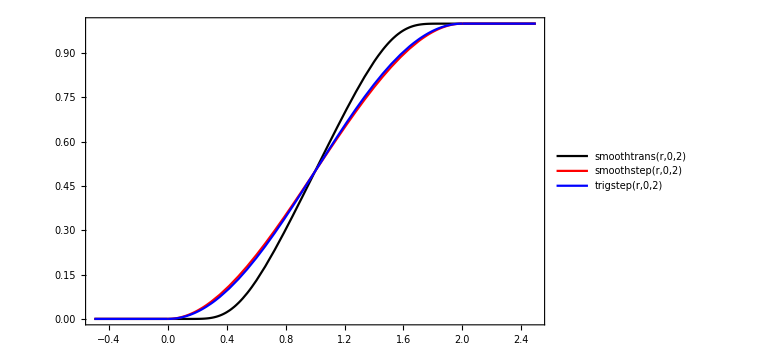

```mathematica
ClearAll[smoothtrans]
smoothtrans[r_,r0_,rh_]:=Module[
{
y,
fy,
omy,
fomy
},

y=(r-r0)/(rh-r0);
If[y>0,fy=Exp[-1.0/y],fy=0.0];

omy=1.0-y;
If[omy>0.0,fomy=Exp[-1.0/omy],fomy=0.0];

Return[fy/(fy+fomy)];
];

ClearAll[trigstep];
trigstep[r_,r0_,rh_]:=Piecewise[
{
{0,r<r0},
{1/2+1/2 Cos[(π/(rh-r0))(r-r0)+π],r0≤r≤rh},
{1,r>rh}
}
];

ClearAll[polystep];
polystep[r_,r0_,rh_]:=Piecewise[
{
{0,r<r0},
{1,r>rh},
{InterpolatingPolynomial[Table[{x,1/2+1/2 Cos[(π/(rh-r0))(x-r0)+π]},{x,r0,rh,(rh-r0)/3}],r],True}
}
];

ClearAll[smoothstep];
smoothstep[r_,r0_,rh_]:=Piecewise[
{
{1,r>rh},
{0,r<r0},
{((r-r0)/(rh-r0))*((r-r0)/(rh-r0))*(3-2*((r-r0)/(rh-r0))),True}
}
];

Plot[{smoothtrans[r,0,2],smoothstep[r,0,2],trigstep[r,0,2]},
{r,-0.5,2.5},
PlotStyle->{Directive[Black,Thick],Directive[Red,Thick],Directive[Blue,Thick]},
PlotRange->Full,
ImageSize->Large,
Axes->False,
Frame->True,
PlotLegends->"Expressions"
]

ClearAll[smoothtrans,smoothstep,trigstep,polystep];
```

# Gaussian initial data

```mathematica
On[Assert];

ClearAll[realSphericalHarmonics];
realSphericalHarmonics[l_,m_,x_,y_,z_]:=
Piecewise[
{
{(-1)^m √((2l+1)/(4π)((l-m)!)/((l+m)!))LegendreP[l,m,z/(√(x^2+y^2+z^2))]Cos[m*ArcTan[x,y]],m≥0},
{(-1)^m √((2l+1)/(4π)((l-Abs[m])!)/((l+Abs[m])!))LegendreP[l,Abs[m],z/(√(x^2+y^2+z^2))]Sin[Abs[m]*ArcTan[x,y]],m<0}
}
];

ClearAll[baseGaussian,baseGaussianDX];
baseGaussian[x_,sigma_]:=Exp[-1/2*(x/sigma)^2];
baseGaussianDX[x_,sigma_]:=-x/sigma^2*baseGaussian[x,sigma];

ClearAll[gaussianSolution,smallrGaussianSolution];
gaussianSolution[r_,t_,sigma_]:=(baseGaussian[r-t,sigma]-baseGaussian[r+t,sigma])/r;
smallrGaussianSolution[r_,t_,sigma_]:=2*t/sigma^2*baseGaussian[t,sigma];

ClearAll[gaussianSolutionDT,smallrgaussianSolutionDT];
gaussianSolutionDT[r_,t_,sigma_]:=-(baseGaussianDX[r-t,sigma]+baseGaussianDX[r+t,sigma])/r;
smallrgaussianSolutionDT[r_,t_,sigma_]:=2*(sigma^2-t^2)/sigma^4*baseGaussian[t,sigma];

Assert[FullSimplify[D[baseGaussian[x,sigma],x]==baseGaussianDX[x,sigma]]]
Assert[FullSimplify[Limit[gaussianSolution[r,t,sigma],r->0]==smallrGaussianSolution[r,t,sigma]]]
Assert[FullSimplify[D[gaussianSolution[r,t,sigma],t]==gaussianSolutionDT[r,t,sigma]]]
Assert[FullSimplify[Limit[D[gaussianSolution[r,t,sigma],t],r->0]==smallrgaussianSolutionDT[r,t,sigma]]]

ClearAll[multipolarGaussian];
multipolarGaussian[x_,y_,z_]:=Sum[c[l,m]realSphericalHarmonics[l,m,x-x0,y-y0,z-z0],{l,0,2},{m,-l,l}]*baseGaussian[Sqrt[(x-x0)^2+(y-y0)^2+(z-z0)^2]-R0,sigma];

Off[Assert];
```

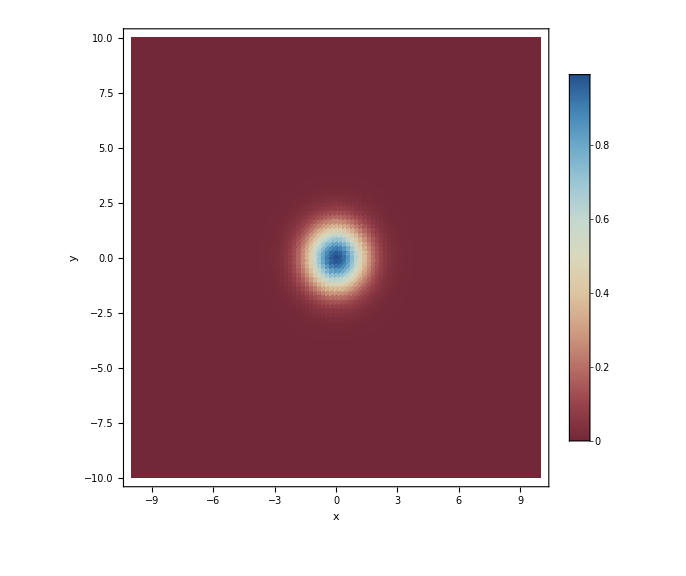

```mathematica
ClearAll[c];

c[0,0]=2*Sqrt[π];

c[1,-1]=0;
c[1,0]=0;
c[1,1]=0;

c[2,-2]=0;
c[2,-1]=0;
c[2,0]=0;
c[2,1]=0;
c[2,2]=0;

ClearAll[sigma,R0];
sigma=1;
R0=0;

ClearAll[x0,y0,z0];
x0=0;
y0=0;
z0=0;

DensityPlot[
multipolarGaussian[x,y,0],
{x,-10,10},
{y,-10,10},
PlotRange->{{-10,10},{-10,10},Full},
ColorFunction->"RedBlueTones",
PlotLegends->Automatic,
ImageSize->Large,
PlotPoints->100,
AxesLabel->{"x","y","f(x,y)"}
]

ClearAll[c];
ClearAll[sigma,R0];
ClearAll[x0,y0,z0];
```

# Local to global derivatives

## Obtaining the derivative to index correspondance

```mathematica
ClearAll[Jac,DJac];
Jac=Simplify[Outer[D,{a[x,y,z],b[x,y,z],c[x,y,z]},{x,y,z}]];
DJac=Simplify[Outer[D,Jac,{x,y,z}]];

MatrixForm[Jac]
MatrixForm[DJac]
```

(a^(1,0,0)[x,y,z] | a^(0,1,0)[x,y,z] | a^(0,0,1)[x,y,z]
b^(1,0,0)[x,y,z] | b^(0,1,0)[x,y,z] | b^(0,0,1)[x,y,z]
c^(1,0,0)[x,y,z] | c^(0,1,0)[x,y,z] | c^(0,0,1)[x,y,z])

((a^(2,0,0)[x,y,z]
a^(1,1,0)[x,y,z]
a^(1,0,1)[x,y,z]) | (a^(1,1,0)[x,y,z]
a^(0,2,0)[x,y,z]
a^(0,1,1)[x,y,z]) | (a^(1,0,1)[x,y,z]
a^(0,1,1)[x,y,z]
a^(0,0,2)[x,y,z])
(b^(2,0,0)[x,y,z]
b^(1,1,0)[x,y,z]
b^(1,0,1)[x,y,z]) | (b^(1,1,0)[x,y,z]
b^(0,2,0)[x,y,z]
b^(0,1,1)[x,y,z]) | (b^(1,0,1)[x,y,z]
b^(0,1,1)[x,y,z]
b^(0,0,2)[x,y,z])
(c^(2,0,0)[x,y,z]
c^(1,1,0)[x,y,z]
c^(1,0,1)[x,y,z]) | (c^(1,1,0)[x,y,z]
c^(0,2,0)[x,y,z]
c^(0,1,1)[x,y,z]) | (c^(1,0,1)[x,y,z]
c^(0,1,1)[x,y,z]
c^(0,0,2)[x,y,z]))

## Variable Correspondence

```mathematica
ClearAll[variableRules];
variableRules={
daval->Dorderx[f],
dbval->Dordery[f],
dcval->Dorderz[f],

dadaval->Dorderxx[f],
dadbval->Dorderxy[f],
dadcval->Dorderxz[f],
dbdbval->Dorderyy[f],
dbdcval->Dorderyz[f],
dcdcval->Dorderzz[f],

dadx->J11L,
dady->J12L,
dadz->J13L,

dbdx->J21L,
dbdy->J22L,
dbdz->J23L,

dcdx->J31L,
dcdy->J32L,
dcdz->J33L,

ddadxdx->J111L,
ddbdxdx->J211L,
ddcdxdx->J311L,

ddadxdy->J112L,
ddbdxdy->J212L,
ddcdxdy->J312L,

ddadxdz->J113L,
ddbdxdz->J213L,
ddcdxdz->J313L,

ddadydy->J122L,
ddbdydy->J222L,
ddcdydy->J322L,

ddadydz->J123L,
ddbdydz->J223L,
ddcdydz->J323L,

ddadzdz->J133L,
ddbdzdz->J233L,
ddcdzdz->J333L
};
```

## Second Derivatives

```mathematica
Block[{ddval},
ddval=ddadxdx*daval+ddbdxdx*dbval+ddcdxdx*dcval;
ddval+=dadx*dadx*dadaval+dbdx*dbdx*dbdbval+dcdx*dcdx*dcdcval+2*dadx*dbdx*dadbval+2*dadx*dcdx*dadcval+2*dbdx*dcdx*dbdcval;
StringReplace["#define global_Dxx(order, f) ("<>ToString[FullSimplify[ddval//.variableRules],CForm]<>")","Dorder"->"D##order##"]
]

Block[{ddval},
ddval=ddadxdy*daval+ddbdxdy*dbval+ddcdxdy*dcval;
ddval+=dadx*dady*dadaval+dbdx*dbdy*dbdbval+dcdx*dcdy*dcdcval+(dadx*dbdy+dady*dbdx)*dadbval+(dadx*dcdy+dady*dcdx)*dadcval+(dbdx*dcdy+dbdy*dcdx)*dbdcval;
StringReplace["#define global_Dxy(order, f) ("<>ToString[FullSimplify[ddval//.variableRules],CForm]<>")","Dorder"->"D##order##"]
]

Block[{ddval},
ddval=ddadxdz*daval+ddbdxdz*dbval+ddcdxdz*dcval;
ddval+=dadx*dadz*dadaval+dbdx*dbdz*dbdbval+dcdx*dcdz*dcdcval+(dadx*dbdz+dadz*dbdx)*dadbval+(dadx*dcdz+dadz*dcdx)*dadcval+(dbdx*dcdz+dbdz*dcdx)*dbdcval;
StringReplace["#define global_Dxz(order, f) ("<>ToString[FullSimplify[ddval//.variableRules],CForm]<>")","Dorder"->"D##order##"]
]

Block[{ddval},
ddval=ddadydy*daval+ddbdydy*dbval+ddcdydy*dcval;
ddval+=dady*dady*dadaval+dbdy*dbdy*dbdbval+dcdy*dcdy*dcdcval+2*dady*dbdy*dadbval+2*dady*dcdy*dadcval+2*dbdy*dcdy*dbdcval;
StringReplace["#define global_Dyy(order, f) ("<>ToString[FullSimplify[ddval//.variableRules],CForm]<>")","Dorder"->"D##order##"]
]

Block[{ddval},
ddval=ddadydz*daval+ddbdydz*dbval+ddcdydz*dcval;
ddval+=dady*dadz*dadaval+dbdy*dbdz*dbdbval+dcdy*dcdz*dcdcval+(dady*dbdz+dadz*dbdy)*dadbval+(dady*dcdz+dadz*dcdy)*dadcval+(dbdy*dcdz+dbdz*dcdy)*dbdcval;
StringReplace["#define global_Dyz(order, f) ("<>ToString[FullSimplify[ddval//.variableRules],CForm]<>")","Dorder"->"D##order##"]
]

Block[{ddval},
ddval=ddadzdz*daval+ddbdzdz*dbval+ddcdzdz*dcval;
ddval+=dadz*dadz*dadaval+dbdz*dbdz*dbdbval+dcdz*dcdz*dcdcval+2*dadz*dbdz*dadbval+2*dadz*dcdz*dadcval+2*dbdz*dcdz*dbdcval;
StringReplace["#define global_Dzz(order, f) ("<>ToString[FullSimplify[ddval//.variableRules],CForm]<>")","Dorder"->"D##order##"]
]
```

#define global_Dxx(order, f) (J111L*D##order##x(f) + Power(J11L,2)*D##order##xx(f) + 2*J11L*J21L*D##order##xy(f) + J211L*D##order##y(f) + Power(J21L,2)*D##order##yy(f) + J311L*D##order##z(f) + J31L*(2*J11L*D##order##xz(f) + 2*J21L*D##order##yz(f) + J31L*D##order##zz(f)))

#define global_Dxy(order, f) (J112L*D##order##x(f) + J11L*J12L*D##order##xx(f) + J12L*J21L*D##order##xy(f) + J11L*J22L*D##order##xy(f) + J12L*J31L*D##order##xz(f) + J11L*J32L*D##order##xz(f) + J212L*D##order##y(f) + J21L*J22L*D##order##yy(f) + J22L*J31L*D##order##yz(f) + J21L*J32L*D##order##yz(f) + J312L*D##order##z(f) + J31L*J32L*D##order##zz(f))

#define global_Dxz(order, f) (J113L*D##order##x(f) + J11L*J13L*D##order##xx(f) + J13L*J21L*D##order##xy(f) + J11L*J23L*D##order##xy(f) + J13L*J31L*D##order##xz(f) + J11L*J33L*D##order##xz(f) + J213L*D##order##y(f) + J21L*J23L*D##order##yy(f) + J23L*J31L*D##order##yz(f) + J21L*J33L*D##order##yz(f) + J313L*D##order##z(f) + J31L*J33L*D##order##zz(f))

#define global_Dyy(order, f) (J122L*D##order##x(f) + Power(J12L,2)*D##order##xx(f) + 2*J12L*J22L*D##order##xy(f) + J222L*D##order##y(f) + Power(J22L,2)*D##order##yy(f) + J322L*D##order##z(f) + J32L*(2*J12L*D##order##xz(f) + 2*J22L*D##order##yz(f) + J32L*D##order##zz(f)))

#define global_Dyz(order, f) (J123L*D##order##x(f) + J12L*J13L*D##order##xx(f) + J13L*J22L*D##order##xy(f) + J12L*J23L*D##order##xy(f) + J13L*J32L*D##order##xz(f) + J12L*J33L*D##order##xz(f) + J223L*D##order##y(f) + J22L*J23L*D##order##yy(f) + J23L*J32L*D##order##yz(f) + J22L*J33L*D##order##yz(f) + J323L*D##order##z(f) + J32L*J33L*D##order##zz(f))

#define global_Dzz(order, f) (J133L*D##order##x(f) + Power(J13L,2)*D##order##xx(f) + 2*J13L*J23L*D##order##xy(f) + J233L*D##order##y(f) + Power(J23L,2)*D##order##yy(f) + J333L*D##order##z(f) + J33L*(2*J13L*D##order##xz(f) + 2*J23L*D##order##yz(f) + J33L*D##order##zz(f)))